```mathematica
ClearAll[a,b,c,l,d];
(*a=b=c=0;*)
a=b=c=0.9;
d=d;
l=a b+b c+a c;
m=a+b+c;

β0=d ;
β1=1/12(m+5l-23a b c+5)-3β0;
β2=1/12(-8m+8 l+16 a b c-16)+3 β0 ;
β3=1/12(-5m-l-5*a b c+23)-β0;
α0=a b c;
α1=-(l+a b c);
α2=m+l;
α3=-(m+1);
α4=1;
ρ[z_]:=α0+α1 z+α2 z^2+α3 z^3+α4 z^4;
σ[z_]:=β0+β1 z+β2 z^2+β3 z^3;
zz=Exp[I ξ];
μ=ρ[zz]/σ[zz]
yyy=FullSimplify[μ/.ξ->π]
Manipulate[
ParametricPlot[{Re[μ],Im[μ]}/.d->α0
,{ξ,0,2π}
,MaxRecursion->3
,PlotPoints-> 100
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All,ImageSize->Large]
,{α0,-0.9,0.8}
]
```

(0.729-3.159 ⅇ^(ⅈ ξ)+5.13 ⅇ^(2 ⅈ ξ)-3.7 ⅇ^(3 ⅈ ξ)+ⅇ^(4 ⅈ ξ))/(d+(0.256917-3 d) ⅇ^(ⅈ ξ)+(-0.541333+3 d) ⅇ^(2 ⅈ ξ)+(0.285417-d) ⅇ^(3 ⅈ ξ))

1.71475/(-0.135458+d)

```mathematica
immu=ComplexExpand[Im[μ]]//FullSimplify
dimmu=D[immu,ξ]/.ξ->π
sol=First@Solve[dimmu==0,d]
```

((0.+6.50521×10^-20 ⅈ) Cos[3 ξ]-(0.+7.40149×10^-18 ⅈ) d Cos[4 ξ]+(-0.0000980165+0.466617 d+(0.000156825-0.933254 d) Cos[ξ]) Sin[ξ]+(-0.0000196029+0.19999 d) Sin[3 ξ]-0.0333333 d Sin[4 ξ])/(-0.000176429+(0.0197807-0.666667 d) d+(0.000235239+d (-0.029691+1. d)) Cos[ξ]+(-0.0000588091+(0.0119003-0.4 d) d) Cos[2 ξ]+(-0.00199003+0.0666667 d) d Cos[3 ξ])

((0.000254842+0. ⅈ)-3 (-0.0000196029+0.19999 d)-1.5332 d)/(-0.000470477+(0.0197807-0.666667 d) d+(0.0119003-0.4 d) d-(-0.00199003+0.0666667 d) d-d (-0.029691+1. d))

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{d→0.000147035}

```mathematica
A={α0,α1,α2,α3,α4,0};
B={β0,β1,β2,β3,0};
k=4;p=3;
C111=1/((p+1)!)(∑_(i=0)^k A[[i+1]]*i^(p+1)-(p+1)*∑_(i=0)^k B[[i+1]]*i^p)/(∑_(i=0)^k B[[i+1]])//Simplify(*C*)
```

985125.+1.×10^6 d

{0.99→0.99,0.99→0.99,0.99→0.99,2.9403→2.9403,2.97→2.97}

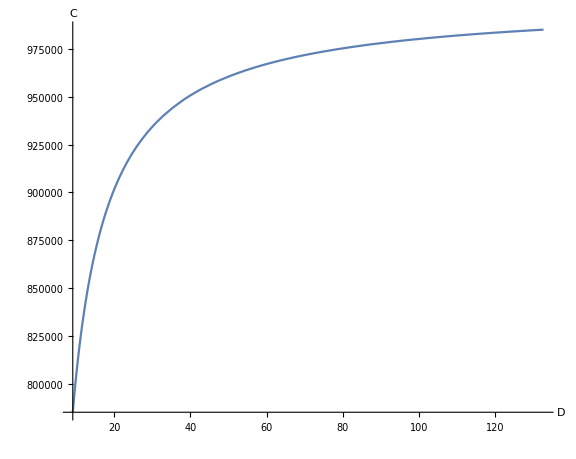

```mathematica
param={a->0.99,b->0.99,c->0.99,
l->a*b+b*c+a*c,
m->a+b+c}
ccc=C111/.param;
ddd=yyy/.param;
ParametricPlot[Evaluate[{Abs[ddd],ccc}],{d,-0.2,0},PlotRange->All,ImageSize->Large,AspectRatio->0.8,LabelStyle->{16,GrayLevel[0]},AxesLabel->{Style[D,Medium],Style[C,Medium]}]
```

```mathematica
d=0.012318;
ddd
```

ddd

```mathematica
1.71475/-0.13545833333333335
```

-12.6589

```mathematica
-17.15404342821153/1000
```

-0.017154

```mathematica
-Log[0.054]
```

2.91877